```mathematica
proc=ItoProcess[{ⅆx[t]== ⅆw1[t],ⅆy[t]==ⅆw2[t],ⅆ i12[t]==y[t]ⅆ w1[t],ⅆ i21[t]==x[t]ⅆ w2[t]},{x[t],y[t],i12[t],i21[t]},{{x,y,i12,i21},{0,0,0,0}},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}]
```

ItoProcess[{{0,0,0,0},{{1,0},{0,1},{y[t],0},{0,x[t]}},{x[t],y[t],i12[t],i21[t]}},{{x,y,i12,i21},{0,0,0,0}},{t,0}]

```mathematica
fun=RandomFunction[proc,{0,100,1},50000]
```

TemporalData[<<50000>>]

```mathematica
integ=fun["SliceData",100];
```

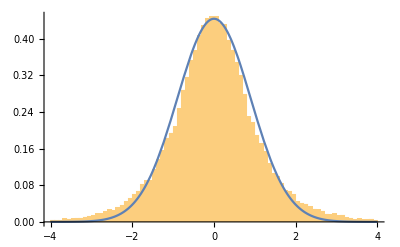

```mathematica
Show[
Histogram[((#[[3]]-#[[4]])&/@integ)/90,{-4,4,0.1},"PDF"],
Plot[PDF[NormalDistribution[0,0.9],x],{x,-4,4}]
]
```

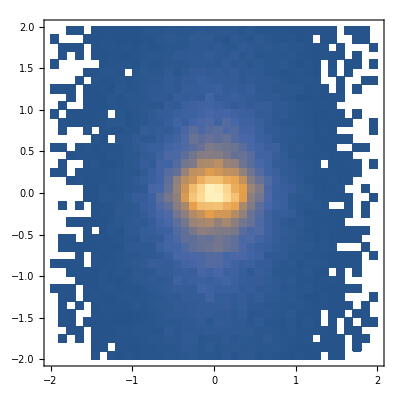

```mathematica
DensityHistogram[{(#[[3]]-#[[4]])/200,(#[[3]]+#[[4]])/100}&/@integ,{-2,2,0.1}]
```